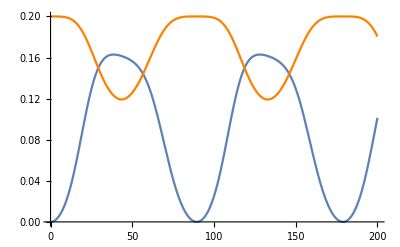

```mathematica
ClearAll["Global`*"];
subtractAngles[a1_,a2_]:=(
d=Abs[a1-a2];
Return[Min[d,2*Pi-d]];
);
angularError[vec_,vecError_,rx_,ry_,rz_,t_,i_]:=(
sphericalVec=ToSphericalCoordinates[vec.MatrixPower[N[EulerMatrix[{rx,ry,rz}]],t]];
sphericalVecError=ToSphericalCoordinates[vecError.MatrixPower[N[EulerMatrix[{rx,ry,rz}]],t]];
Return[subtractAngles[sphericalVec[[i]],sphericalVecError[[i]]]];
);
elevationErrorPlot=Plot[angularError[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],Pi/100,Pi/100,Pi/100,t,2],{t,0,200},PlotStyle->Orange];
azimuthalErrorPlot=Plot[angularError[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],Pi/100,Pi/100,Pi/100,t,3],{t,0,200}];
Show[azimuthalErrorPlot,elevationErrorPlot,PlotRange->All]
```

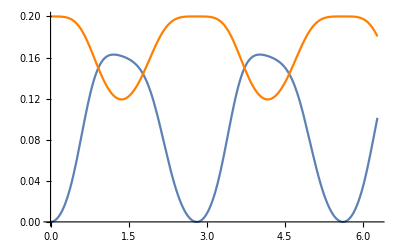

```mathematica
SP[t_]:={{Cos[√5 t],-((2 Sin[√5 t])/(√5)),Sin[√5 t]/(√5)},{(2 Sin[√5 t])/(√5),(1/5) (1+4 Cos[√5 t]),-(2/5) (-1+Cos[√5 t])},{-(Sin[√5 t]/(√5)),-(2/5) (-1+Cos[√5 t]),(1/5) (4+Cos[√5 t])}};
angularErrorSimplified[vec_,vecError_,t_,i_]:=(
sphericalVec=ToSphericalCoordinates[vec.SP[t]];
sphericalVecError=ToSphericalCoordinates[vecError.SP[t]];
Return[subtractAngles[sphericalVec[[i]],sphericalVecError[[i]]]];
);
elevationErrorPlotSimplified=Plot[angularErrorSimplified[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],t,2],{t,0,2Pi},PlotStyle->Orange];
azimuthalErrorPlotSimplified=Plot[angularErrorSimplified[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],t,3],{t,0,2Pi}];
Show[azimuthalErrorPlotSimplified,elevationErrorPlotSimplified,PlotRange->All]
```

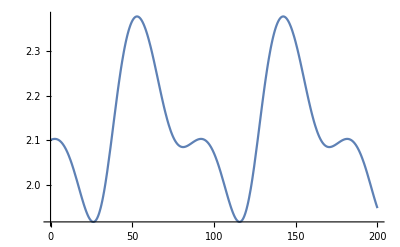

```mathematica
azimuthalError[errx_,erry_,errz_,s_,t_]:=(mp=MatrixPower[N[EulerMatrix[{2 Pi/s,2 Pi/s,2 Pi/s}]],t];
sphericalVec=ToSphericalCoordinates[{1,0,0}.mp];
sphericalVecError=ToSphericalCoordinates[{1,0,0}.EulerMatrix[{errx,erry,errz}].mp];
Return[subtractAngles[sphericalVec[[3]],sphericalVecError[[3]]]];);
Plot[azimuthalError[1.5,2,0.5,200,t],{t,0,200},PlotRange->All]
```

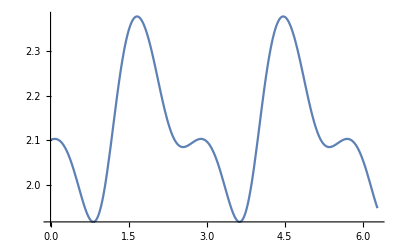

```mathematica
ClearAll["Global`*"];
subtractAngles[a1_,a2_]:=(
d=Abs[a1-a2];
Return[Min[d,2*Pi-d]];
);
SP[t_]:={{Cos[√5 t],-(2 Sin[√5 t])/(√5),Sin[√5 t]/(√5)},{(2 Sin[√5 t])/(√5),1/5 (1+4 Cos[√5 t]),-2/5 (-1+Cos[√5 t])},{-Sin[√5 t]/(√5),-2/5 (-1+Cos[√5 t]),1/5 (4+Cos[√5 t])}};
azimuthalErrorSimplified[errx_,erry_,errz_,t_]:=(
sphericalVec=ToSphericalCoordinates[{1,0,0}.SP[t]];
sphericalVecError=ToSphericalCoordinates[{1,0,0}.EulerMatrix[{errx,erry,errz}].SP[t]];
Return[subtractAngles[sphericalVec[[3]],sphericalVecError[[3]]]];);
Plot[azimuthalErrorSimplified[1.5,2,0.5,t],{t,0,2Pi},PlotRange->All]
```